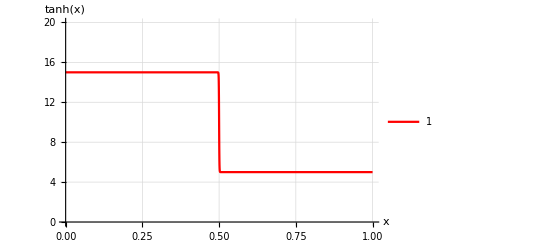

```mathematica
Plot[10+5(-Tanh[(x+1)/0.001]Tanh[(x-0.5)/0.001]),{x,0,1},PlotRange-> {{0,1},{0,20}},AxesLabel->{"x","tanh(x)"},GridLines->Automatic,PlotStyle->Red,PlotLegends->{"1"}]
```

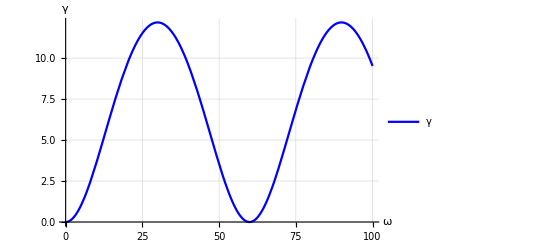

```mathematica
(*SEE REAL NUMBERS FOR THESE PARAMETERS*)
u=60;
sa=50;
sb =100;
Z=(sb^2+sa^2)/(2sb sa);
Lb=5;
La=5;
Tb=Lb(sb^5/(sb^6-u^6));
Ta=La(sa^5/(sa^6-u^6));
T0a = La/sa;
Show[Plot[(1+u^3/sa^3)/T0a Log[1+(Z^2-1)(Sin[x Tb])^2],{x,0,100},PlotRange->All,AxesLabel->{"ω","γ"},GridLines->Automatic,PlotStyle->Blue,PlotLegends->{"γ"}]]
```